## regression model

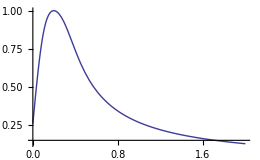

```mathematica
dat=ParallelTable[{s,MAPKpp[0]/MAXMAPKPP}/.runsim[p4[_]->0,p2->0,Stot->s,p1[_]->100],{s,0.0,2.0,0.01}];
erk=Interpolation[dat];
Plot[erk[t],{t,0,2}]
```

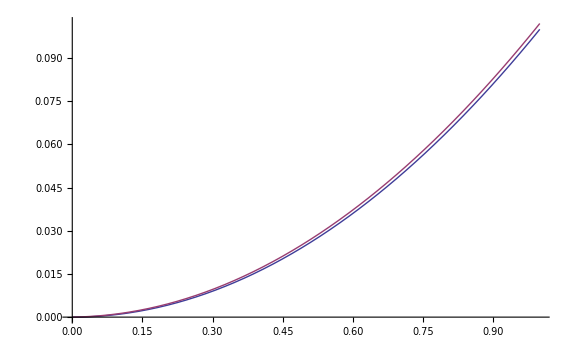

-Graphics3D-

```mathematica
dX=0.01;
maxdose=1.0;
S=Function[{stot,l,x,g},With[{δ=g*maxdose(l+dX*x)},
Clip[stot*δ^2,{0,2}]
]];
Plot[{S[0.1,d,0,1],S[0.1,d,1,1]},{d,0,1}]
Plot3D[S[t,d,0,1],{d,0,1},{t,0.01,0.2},AxesLabel->{"Dose","Stot","Sves"}]
```

```mathematica
Srng=Range[0,0.4,0.01];
qsrng=Quantile[Srng,Range[0,1,0.25]];
{avgErk,avgMI}=Transpose@Map[Function[t,{Mean[erk[S[t,#,0]]&/@lenX],
Mean[Map[erk[S[t,#,1]]-erk[S[t,#,0]]&,lenX]]}],Srng];
{avgErk,avgMI}=Transpose[{Srng,#}]&/@{avgErk,avgMI/Max[Abs[avgMI]]};
```

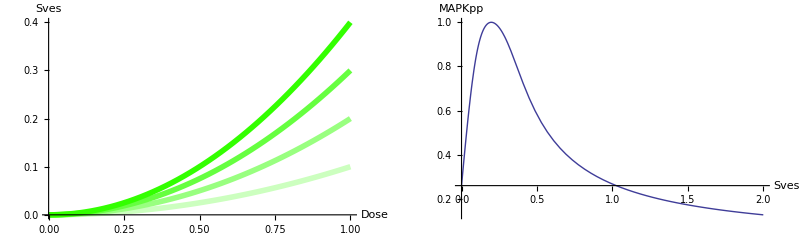

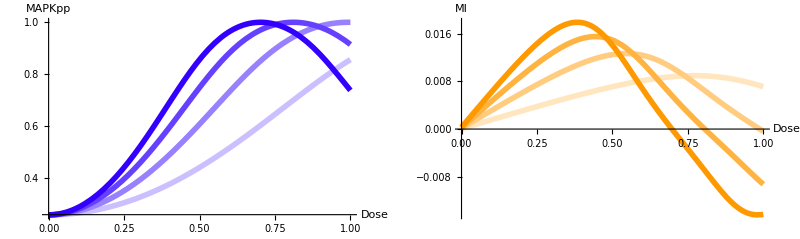

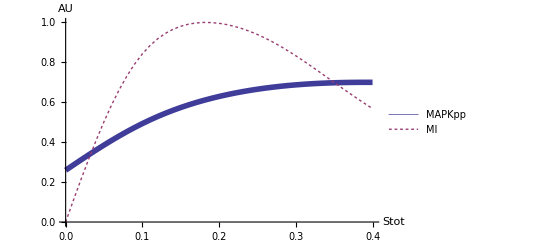

```mathematica
GraphicsRow[{
Plot[S[#,d,0]&/@qsrng//Evaluate,{d,0,1},AxesLabel->{"Dose","Sves"},PlotStyle->({{Thickness[0.01],Hue[0.3,#,1]}}&/@Rescale[qsrng])],
Plot[erk[t],{t,0,2},AxesLabel->{"Sves","MAPKpp"},AxesOrigin->{0,0.26}]}]
GraphicsRow[{
Plot[erk[S[#,d,0]]&/@qsrng//Evaluate,{d,0,1},PlotRange->All,PlotStyle->({{Thickness[0.01],Hue[0.7,#,1]}}&/@Rescale[qsrng]),AxesLabel->{"Dose","MAPKpp"}],
Plot[(erk[S[#,d,1]]-erk[S[#,d,0]])&/@qsrng//Evaluate,{d,0,1},PlotRange->All,PlotStyle->({{Thickness[0.01],Hue[0.1,#,1]}}&/@Rescale[qsrng]),AxesLabel->{"Dose","MI"}]
}]
ListLinePlot[{avgErk,avgMI},PlotStyle->{Thickness[0.01],Dashing[Tiny]},PlotLegends->{"MAPKpp","MI"},AxesLabel->{"Stot","AU"}]
```

```mathematica
grad=Range[0,1.0,0.05]//Chop
```

{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

```mathematica
MIfunc=Function[{stot,g},Map[erk[S[stot,#,1,g]]-erk[S[stot,#,0,g]]&,lenX]]
```

Function[{stot,g},(erk[S[stot,#1,1,g]]-erk[S[stot,#1,0,g]]&)/@lenX]

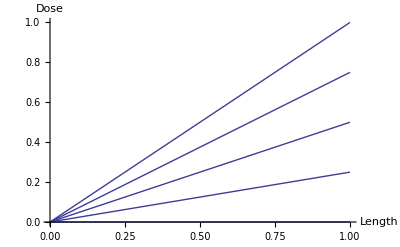

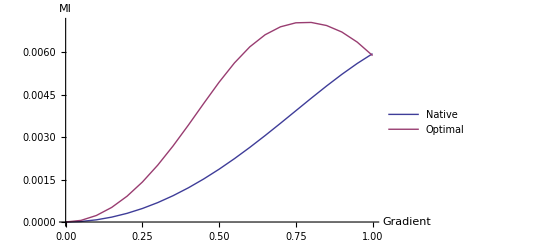

```mathematica
StotNative=0.1;
StotOptimal=0.3;
Plot[Quantile[grad,Range[0,1,0.25]]*maxdose(l),{l,0,1},AxesLabel->{"Length","Dose"}]
ListLinePlot[{
{#,Mean[MIfunc[StotNative,#]]}&/@grad,
{#,Mean[MIfunc[StotOptimal,#]]}&/@grad},AxesLabel->{"Gradient","MI"},PlotLegends->{"Native","Optimal"}]
```

## sigmoid product bell curve

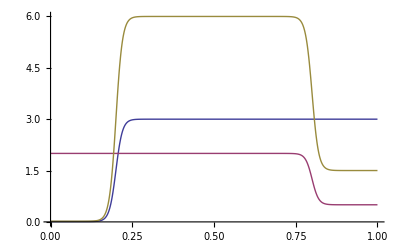

```mathematica
b1=((b-d)/(1+Exp[(a-s)c])+d)/.{a->0.2,c->100,b->3,d->0.01};
b2=((b-d)/(1+Exp[(s-a)c])+d)/.{a->0.8,c->100,b->2,d->0.5};
Plot[{b1,b2,b1 b2},{s,0,1}]
```

## dynamic

```mathematica
inputθ0[]
```

### old θ0

```mathematica
θ0={10,1.,0.1,0.,111.,6.,0.4,1.1,5.,1.,9.,90.,0.01,0.0001};
```

```mathematica
θ0={3.104707774719503,1.0497295760247896,0.10935569516958227,0.031203421377739658,115.66687569390423,5.386378348968132,0.38111485253554317,1.1205801867316698,4.658062694250514,0.9491324623113798,8.312987883211724,90.24714510283111,0.009918375869260063,0.00009337733142904706};
```

```mathematica
θ0={3.,1.,0.1,0.,115.,5.5,0.4,1.1,5.,1.,5.,90.,0.01,0.0001};
```

```mathematica
θ0={2.901440967566177,1.0293931895924457,0.10466290551680711,0.009309589734646179,116.59953216191134,5.426691958249558,0.03635671167218997,2.2187421775215617,4.560371205069806,0.9818422905647498,4.035781078320655,45.169237978357124,0.009674146549885613,0.00012827148106897337};
```

```mathematica
θ0={2.633019474658832,1.0272215234837838,0.10467874711582693,0.016164589460779335,119.30358853399952,5.429508816141995,0.036506229650460346,2.231363605129936,4.570779721044903,0.9697094393590681,4.035781078320655,45.27498282944627,0.009677927823576151,0.0001247650919062626};
```

```mathematica
θ0={6.928593610371945,0.9991417386457014,0.10100367350891862,0.10025147204714309,111.11446446979507,5.877246692817733,0.3970732533493151,1.4900484349796603,4.241289068469159,1.0044048672736243,9.,88.14636882724636,0.009258111009708072,0.00009607633823434401};
```

### new θ0

```mathematica
θ0={6.928593610371945,0.9991417386457014,0.10100367350891862,0.10025147204714309,111.11446446979507,5.877246692817733,0.3970732533493151,1.4900484349796603,4.241289068469159,1.0044048672736243,9.,88.14636882724636,0.009258111009708072,0.00009607633823434401};
```

```mathematica
θ0={10.556306579891462,1.0016261547846619,0.10175213407377859,0.009035578966831005,112.10826806596532,5.975587149452891,0.3961381194367518,1.1317736596950516,4.20535223275372,1.0009909478971593,8.995973509584626,89.84318942536449,0.010065409564079385,0.00009472926341647595};
```

```mathematica
θ0={11.20162736338172,1.0078058007843143,0.1023340311797417,0.007276110016365396,130.84104308282426,6.005648009684505,0.34759360807392925,1.1298302027052798,4.137042552869907,1.0340417771966854,9.,89.6261130181519,0.010055820593925796,0.00009200626910548427};
```

```mathematica
θ0={8.076964789774616,0.9683311602844228,0.09630260644909382,0.0024446040253360375,106.70077044583444,1.5002850175387201,1.500263359633233,1.199676210067386,5.027804532625143,1.1996495038324484,3.,80.11993203230725,0.009807511230398656,0.00009899950675672363};
```

```mathematica
viz
vizLossDiff[]
vizLossBar
```

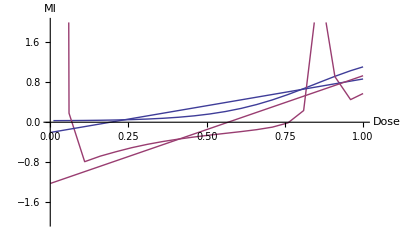

```mathematica
Show[ListLinePlot[{λ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotRange->2*10^0{-1,1},AxesLabel->{"Dose","MI"}],
Plot[{equNative,equOE},{x,0,1}]
]
```

```mathematica
θ0=Lhist[[300,2]]
Loss[θ0]
```

{10.1059,1.00057,0.101102,0.00953495,111.708,6.02071,0.4007,1.1261,4.20516,1.00202,8.99597,89.8058,0.0099956,0.0000973549}

4291.95

## other plots

```mathematica
θ0={8.088671158960132,0.9680869802065624,0.0962191105644522,0.002392737301719244,107.08475086683993,6.1430109284879455,0.4183536518812163,1.1147803659165367,4.9933662187516985,1.027420205695692,3.,90.06931519283201,0.01006738098574038,0.00009878171106501613};
```

```mathematica
θ0={8.088671158960132,0.9680869802065624,0.0962191105644522,0.002392737301719244,107.08475086683993,1.5,1.5,1.2,4.9933662187516985,1.2,3.,80.069315192832,0.01,0.0001};
```

```mathematica
inputθ0[]
```

| θ0 | -10% | +10% | -1% | +1%
p4b |  | - | + | - | +
p2 |  | - | + | - | +
p3a |  | - | + | - | +
p3b |  | - | + | - | +
p3c |  | - | + | - | +
p3d |  | - | + | - | +
p3e |  | - | + | - | +
p3f |  | - | + | - | +
p5 |  | - | + | - | +
StotNative |  | - | + | - | +
StotOpt |  | - | + | - | +
StotOE |  | - | + | - | +
maxdose |  | - | + | - | +
dX |  | - | + | - | +

```mathematica
Dynamic[Block[{dat},
dat=myrunsim[{},gradient->{1}];
dat=Transpose[dat,{2,3,1,4}];
dat=Flatten[dat,1];
Column[{θ0,figs[dat]}]
],TrackedSymbols:>{θ0},SynchronousUpdating->False]
```

```mathematica
fig2[]:=Block[{dat},
dat=myrunsim[{},lengthX->Select[lenX,#>0.2&],gradient->{1},slevel->(Range[StotNative,StotOE,(StotOE-StotNative)/30.]/.pθ0)];
Block[{MI,ERK},
ERK={Stot/StotNative,(MAPKpp[0]+MAPKpp[1])/(2*MAXMAPKPP)}/.dat//Transpose[#,{3,2,1}]&//Flatten[#,1]&//Mean;
MI={Stot/StotNative,MI}//.dat//Transpose[#,{3,2,1}]&//Flatten[#,1]&//Mean;
ListPlot[{ERKᵀ/{1,Max[ERK[[All,2]]]}//Transpose,MIᵀ/{1,Max[MI[[All,2]]]}//Transpose},Joined->True,PlotRange->{-0.5,1},Filling->Axis,AxesOrigin->{StotOpt/.pθ0,0},AxesLabel->{"Scaffold","AU"},PlotStyle->Thick,ImageSize->Full
]]]
```

```mathematica
fig3[]:=Block[{dat},
dat=myrunsim[{},lengthX->Drop[lenX,4],gradient->Chop@Range[0.1,1.0,0.1],slevel->({StotNative,StotOpt}/.pθ0)];
ListLinePlot[{γ,MI}//.dat//Transpose//Mean,PlotMarkers->Automatic,AxesLabel->{"Gradient","MI"},PlotRange->{{0,1},All},Filling->Axis,ImageSize->Full]
]
```

```mathematica
θ0={10,1.,0.1,0,111,6,0.4,1.1,5.,1.,4.,80,0.01,0.0001};
```

```mathematica
θ0={10,1.,0.1,0,111.,6.,0.1,2,5.,1.,4.,44.,0.01,0.0001};
```